## Chap 14

### 14-1

#### phase_diagram

```mathematica
Block[{lt=0.8,col,bdy},
col=<|"g"->LightBlue,"l"->Blue,"s"->Green|>;
bdy=<|"sg"->BSplineCurve[{{0,0},{0.1,0},{0.6,0.3},{1,1}}],"lg"->BSplineCurve[{{1,1},{2.5,1.5},{3,3}}],"sl"->Line[{{1,1},{1.1,4}}]|>;
Graphics[{{Lighter[col["s"],lt],FilledCurve[{bdy["sg"],bdy["sl"],Line[{{1.1,4},{0,4}}]}]},
{Lighter[col["l"],lt],FilledCurve[{bdy["lg"],Line[{{3.3,4},{1.1,4}}]}]},
{Lighter[col["g"],lt],FilledCurve[{bdy["sg"],bdy["lg"],Line[{{4,4},{4,0}}]}]},
Block[{dx=0.1,h=1,s=0.3,w=0.7},Translate[{EdgeForm[None],Table[{Blend[Lighter[col[#],lt]&/@{"l","g"},(x+1)/2],Triangle[{{0,0},{s+w x,h},{s+w(x+dx),h}}]},{x,-1,1-dx,dx}]},bdy["lg"][[1,-1]]]],
{Arrowheads[0.05],Arrow[{{0,0},#}]&/@{{4,0},{0,4}},Text["Temperature \!\(T\)",{2,0},{0,1}],Text["Pressure \!\(p\)",{0,2},{0,-1},{0,1}]},
{AbsoluteThickness[1.5],bdy["sg"],bdy["lg"],bdy["sl"]},{AbsolutePointSize[5],Point[{bdy["lg"][[1,1]],bdy["lg"][[1,-1]]}]},
{Text["Solid",{0.5,2}],Text["Liquid",{1.8,2.5}],Text["Gas",{3,1}],
Text[Style["Supercritical\nfluid",12,LineSpacing->{0,12}],{3,3.5}],Text[Style["Triple\npoint",12,LineSpacing->{0,12}],{1,1},{-1,1.2}],
Text[Style["Critical\npoint",12,LineSpacing->{0,12}],{3,3},{-1,1.2}]}},PlotRange->{{-0.5,4},{-0.5,4}},Frame->False,ImageSize->180]]
```

-Graphics-

```mathematica
Block[{lt=0.8,col,bdy},
col=<|"g"->White,"l"->Blue,"s"->Green|>;
bdy=<|"sg"->BSplineCurve[{{0,0},{0.1,0},{0.6,0.3},{1,1}}],"lg"->BSplineCurve[{{1,1},{2.5,1.5},{3,3}}],"sl"->Line[{{1,1},{0.4,4}}]|>;
Graphics[{{Lighter[col["s"],lt],FilledCurve[{bdy["sg"],bdy["sl"],Line[{{0.4,4},{0,4}}]}]},
{Lighter[col["l"],lt],FilledCurve[{bdy["lg"],Line[{{3.3,4},{0.4,4}}]}]},
Block[{dx=0.1,h=1,s=0.3,w=0.4},Translate[{EdgeForm[None],Table[{Blend[Lighter[col[#],lt]&/@{"l","g"},(x+1)/2],Triangle[{{0,0},{s+w x,h},{s+w(x+dx),h}}]},{x,-1,1-dx,dx}]},bdy["lg"][[1,-1]]]],
{Opacity[0.2],AbsoluteThickness[1],Line[{{0,3},{3,3},{3,0}}],Line[{{{0,2},{4,2}},{{0.8,0},{0.8,2}},{{2.5,2},{2.5,0}}}],Line[{{0,1},{1,1},{1,0}}]},
{AbsoluteThickness[1.5],bdy["sg"],bdy["lg"],bdy["sl"]},{AbsolutePointSize[5],Point[{bdy["lg"][[1,1]],bdy["lg"][[1,-1]]}]},
{Text[Style["Ice\n(solid)",LineSpacing->{0, 12}],{0.5,1.3}],Text[Style["Water\n(liquid)",LineSpacing->{0,12}],{1.8,2.5}],Text[Style["Vapor\n(gas)",LineSpacing->{0,12}],{2.5,0.8}],
Text[Style["Supercritical\nfluid",12,LineSpacing->{0,10}],{3,3.5}],Text[Style["Triple\npoint",10,LineSpacing->{0,8}],{1,1},{-1,1.2}],
Text[Style["Critical\npoint",10,LineSpacing->{0,8}],{3,3},{-1,1.2}]}},PlotRange->{{0,4},{0,4}},Frame->True,FrameTicks->{{{{1,"0.6"},{2,"101"},{3,"\!\(2×10\^4\)"}},{{2,"1 atm"}}},{{{0.8,"0"},{1,""},{1.2,Rotate["0.01",-π/4],{0,0}},{2.5,Rotate["100",-π/4]},{3,Rotate["374",-π/4]}},None}},FrameLabel->{"\!\(T\) [°C]","\!\(P\) [kPa]"},ImageSize->250]]
```

-Graphics-

#### piston

```mathematica
Block[{L=2,w=0.3,a=0.05,d=0.8,holo},
holo[txt_]:={{LightBlue,Translate[txt,0.05#]&/@CirclePoints[16]},txt};
Graphics[{{LightBlue,Rectangle[{0,-1},{L,1}],Disk[{L,0},{w,1}]},{AbsoluteThickness[1],Dashed,Circle[{d,0},{w,1}]},{LightBrown,Rectangle[{-a,-1},{0,1}],Disk[{#,0},{w,1}]&/@{-a,0}},{AbsoluteThickness[1],Circle[{-a,0},{w,1}],Circle[{0,0},{w,1},{-π/2,π/2}],},{Translate[Line[{#,0}&/@{-L,L}],{0,#}]&/@{-1,1}},Translate[{AbsoluteThickness[1],Arrowheads[0.04],Arrow[{#,0}&/@{0,d}],Text["\!\(d\)",{d/2,0},{0,1}],Translate[Line[Offset[{0,#}]&/@{-3,3}],{#,0}]&/@{0,d}},{0,-1.2}],
{Arrowheads[0.06],Arrow[{#,0}&/@{-1,0}],Text["\!\(F\&→\)",{-0.5,0},{0,-1}],Text["\!\(A\)",{-a,-0.5}],holo@Text["\!\(Δ,V\)",{0.8d,0}]},Translate[{Point[{0,0}],Text["\!\(p\)",{0,0},{-1.5,0}]},{2d,0}],Translate[{Point[{0,0}],Text["\!\(p=0\)",{0,0},{0,1}]},{-1.2,-0.4}]}]]
```

-Graphics-

### 14-2

#### hydrostatic

```mathematica
Block[{roundline,tank,holo,ah,w=0.5,y1=0.8,y2=0.5,h=0.6},
roundline[pts_,r_:0.2]:=BSplineCurve[Flatten[Riffle[List/@pts,Thread[Table[(#1+r Normalize[#2-#1])&@@@Thread[Through[f[{Most,Rest}][pts]]],{f,{Identity,Reverse}}]]],1]];
tank={{{LightBlue,FilledCurve[#]},#}&@roundline[{{-w,1},{-w,0},{w,0},{w,1}}],Translate[Line[{0,#}&/@{1,1.2}],{#,0}]&/@{-w,w}};
holo[txt_]:={{LightBlue,Translate[txt,0.03#]&/@CirclePoints[16]},txt};
ah[specs_]:=Arrowheads[{0.0001 #1,#2,Graphics[Line[Offset/@{{-6,-2},{-1,0},{-6,2}}]]}&@@@specs];
Graphics[{Translate[{tank,{ah[{{1,1}}],Translate[{{AbsoluteThickness[1],Gray,Arrow[{0,#}&/@{0,y1}]},Point[{0,y1}],Text["\!\(p\_1\)",{0,y1},{1.5,0}],holo@Text["\!\(y\_1\)",{0,y1/2},{0,0}]},{-0.4w,0}],
Translate[{{AbsoluteThickness[1],Gray,Arrow[{0,#}&/@{0,y2}]},Point[{0,y2}],Text["\!\(p\_2\)",{0,y2},{1.5,0}],holo@Text["\!\(y\_2\)",{0,y2/2},{0,0}]},{0.4w,0}]}},{-0.6,0}],Translate[{tank,{{ah[{{-1,0},{1,1}}],AbsoluteThickness[1],Gray,Arrow[{0,#}&/@{1,1-h}]},Point[{0,#}]&/@{1,1-h},Text["\!\(p\_0\)",{0,1},{0,-1}],Text["\!\(p\)",{0,1-h},{2,0}]},holo@Text["\!\(h\)",{0,1-h/2}]},{0.6,0}]},ImageSize->180]]
```

-Graphics-

#### U-tube

```mathematica
Block[{roundline,holo,ah,a=1,w=0.2,h1=0.5,h2=2.6,tube},
roundline[pts_,r_:0.2]:=BSplineCurve[Flatten[Riffle[List/@pts,Thread[Table[(#1+r Normalize[#2-#1])&@@@Thread[Through[f[{Most,Rest}][pts]]],{f,{Identity,Reverse}}]]],1]];
holo[txt_]:={{White,Translate[txt,0.05#]&/@CirclePoints[16]},txt};
ah[specs_]:=Arrowheads[{0.0001 #1,#2,Graphics[Line[Offset/@{{-5,-2},{0,0},{-5,2}}]]}&@@@specs];
tube={{{LightGray,FilledCurve[#]},#}&@{Line@ReIm[(a+w)Exp[ⅈ Range[-π,0,π/24]]],Line[{a+w,#}&/@{0,h1}],Line[{a-w,#}&/@{0.5,0}],Line@ReIm[(a-w)Exp[ⅈ Range[0,-π,-π/24]]]},
{{LightBlue,FilledCurve[#]},#}&@{Line[{-a+w,#}&/@{0,h2}],Line[{-a-w,#}&/@{h2,0}]},Table[Line[{-a+s w,#}&/@{h2,3}],{s,{-1,1}}],Table[Line[{a+s w,#}&/@{h1,3}],{s,{-1,1}}]};
Graphics[{{AbsoluteThickness[1],Dashed,Line[{#,0}&/@{-1.8,1.8}]},tube,{ah[{{-1,0},{1,1}}],AbsoluteThickness[1],Translate[{{Gray,Arrow[{0,#}&/@{0,h2}]},holo@Text["\!\(h\_w\)",{0,h2/2}]},{-a-2.5w,0}],Translate[{{Gray,Arrow[{0,#}&/@{0,h1}]},Text["\!\(h\_Hg\)",{0,h1/2},{-1.5,0}]},{a+2.5w,0}]}},ImageSize->120]]
```

-Graphics-

#### containers

```mathematica
Block[{roundline,tank1,tank2, tank3, tank4},
roundline[pts_,r_:0.2]:=BSplineCurve[Flatten[Riffle[List/@pts,Thread[Table[(#1+r Normalize[#2-#1])&@@@Thread[Through[f[{Most,Rest}][pts]]],{f,{Identity,Reverse}}]]],1]];
{tank1,tank2}=Table[{{{LightYellow,FilledCurve[#]},#}&@roundline[{{-w,1},{-w,0},{w,0},{w,1}}],Translate[Line[{0,#}&/@{1,1.2}],{#,0}]&/@{-w,w}},{w,{1,0.2}}];
tank3=Block[{w1=0.2,w2=0.6},{{{LightYellow,FilledCurve[#]},#}&@roundline[{{-w2,1},{-w1,0},{w1,0},{w2,1}}],Table[Translate[Line[{Sign[w](w2-w1)(#-1),#}&/@{1,1.2}],{w,0}],{w,{-w2,w2}}]}];
tank4=Block[{w1=0.6,w2=0.2},{{{LightYellow,FilledCurve[#]},#}&@roundline[{{-w2,1},{-w1,0},{w1,0},{w2,1}}],Table[Translate[Line[{Sign[w](w2-w1)(#-1),#}&/@{1,1.2}],{w,0}],{w,{-w2,w2}}]}];
Graphics[{Translate[tank1,{0,0}],Translate[tank2,{1.5,0}],Translate[tank3,{2.5,0}],Translate[tank4,{3.6,0}]},ImageSize->220]]
```

-Graphics-

### 14-3

#### barometer

```mathematica
Block[{roundline,holo,ah,w=0.5,h1=0.35,h2=2,a=0.05},
roundline[pts_,r_:0.2]:=BSplineCurve[Flatten[Riffle[List/@pts,Thread[Table[(#1+r Normalize[#2-#1])&@@@Thread[Through[f[{Most,Rest}][pts]]],{f,{Identity,Reverse}}]]],1]];
holo[txt_]:={{White,Translate[txt,0.03#]&/@CirclePoints[16]},txt};
ah[specs_]:=Arrowheads[{0.0001 #1,#2,Graphics[Line[Offset/@{{-5,-2},{0,0},{-5,2}}]]}&@@@specs];
Graphics[{{{LightGray,EdgeForm[None],Rectangle[{-a,0.9h1},{a,h2}]},{{LightGray,FilledCurve[#]},#}&@roundline[{{-w,h1},{-w,0},{w,0},{w,h1}}],Translate[Line[{0,# h1}&/@{1,1.2}],{#,0}]&/@{-w,w},Translate[Line[{0,#}&/@{0.5h1,1.1h2}],{#,0}]&/@{-a,a},Circle[{0,1.1h2},a,{0,π}]},Translate[{Point[{0,0}],Text["\!\(p\_0\)",{0,0},{0,-1}]},{0.5w,h1}],Translate[{{AbsoluteThickness[1],ah[{{-1,0},{1,1}}],Gray,Arrow[{0,#}&/@{h1,h2}]},holo@Text["\!\(h\)",{0,(h1+h2)/2}]},{-a-0.1,0}]},ImageSize->80]]
```

-Graphics-

#### manometer

```mathematica
Block[{roundline,holo,ah,sys,lq,a=0.1,b=0.3,R=0.5,h1=1.5,h2=2},
roundline[pts_,r_:0.2]:=BSplineCurve[Flatten[Riffle[List/@pts,Thread[Table[(#1+r Normalize[#2-#1])&@@@Thread[Through[f[{Most,Rest}][pts]]],{f,{Identity,Reverse}}]]],1]];
holo[txt_]:={{White,Translate[txt,0.03#]&/@CirclePoints[16]},txt};
ah[specs_]:=Arrowheads[{0.0001 #1,#2,Graphics[Line[Offset/@{{-5,-2},{0,0},{-5,2}}]]}&@@@specs];
sys={Circle[{0,0},R+#,{-π,0}]&/@{a,-a},Translate[Line[{0,#}&/@{0,h2}],{R+#,0}]&/@{a,-a},
roundline[{{-R-a,0},{-R-a,h1-a},{-R-a-b,h1-a}},0.1],roundline[{{-R+a,0},{-R+a,h1+a},{-R-a-b,h1+a}}],Translate[{roundline[{{1,a},{1,1},{-1,1},{-1,-1},{1,-1},{1,-a}}]},{-R-a-b-1,h1}]};
lq[h3_,h4_]:={{AbsoluteThickness[1],Gray,{Dashed,Line[{#,h3}&/@{-R-2a,R+4a}],Line[{#,h4}&/@{R-2a,R+4a}]},Translate[{ah[{{1,1}}],Arrow[{0,#}&/@{h3,h4}]},{R+3a,0}],Text[StringTemplate["\!\(h`1`0\)"][If[h3<h4,">","<"]],{R+3a,(h3+h4)/2},{-1.1,0}]},{LightBlue,FilledCurve[{Line@ReIm@Table[(R+a)Exp[ⅈ θ],{θ,-π,0,π/24}],
Line[{R+a,#}&/@{0,h4}],Line[{R-a,#}&/@{h4,0}],
Line@ReIm@Table[(R-a)Exp[ⅈ θ],{θ,0,-π,-π/24}],
Line[{-R+a,#}&/@{0,h3}],Line[{-R-a,#}&/@{h3,0}]}]},
Translate[{Point[{0,0}],holo@Text["\!\(p\)",{a,0},{-2,0}]},{-R,h3}],Translate[{Point[{0,0}],Text["\!\(p\_0\)",{-a,0},{2,0}]},{R,h4}]};
Graphics[{Translate[{lq[0.2,0.8],sys},{0,1.8}],Translate[{lq[0.8,0.2],sys},{0,-1.8}]},ImageSize->180]]
```

-Graphics-

### 14-4

#### hydraulic_lever

```mathematica
Block[{roundline,ah,l=1,h=2,hh=1,a1=0.2,a2=0.6,a3=0.1,ht=0.05},
roundline[pts_,r_:0.2]:=BSplineCurve[Flatten[Riffle[List/@pts,Thread[Table[(#1+r Normalize[#2-#1])&@@@Thread[Through[f[{Most,Rest}][pts]]],{f,{Identity,Reverse}}]]],1]];
ah[specs_]:=Arrowheads[{0.0001 #1,#2,Graphics[Line[Offset/@{{-5,-2},{0,0},{-5,2}}]]}&@@@specs];
Graphics[{{LightYellow,FilledCurve@{roundline[{{-l+a1,hh},{-l+a1,a3},{l-a2,a3},{l-a2,hh}},0.1],Line[{{l-a2,hh},{l+a2,hh}}],roundline[Reverse@{{-l-a1,hh},{-l-a1,-a3},{l+a2,-a3},{l+a2,hh}}],Line[{{-l-a1,hh},{-l+a1,hh}}]}},{LightBrown,Rectangle[{-l-a1,hh},{-l+a1,hh+ht}],Rectangle[{l-a2,hh},{l+a2,hh+ht}]},{AbsoluteThickness[1],Table[Line[{#,y}&/@{-l-a1,-l+a1}],{y,{hh,hh+ht}}],Table[Line[{#,y}&/@{l-a2,l+a2}],{y,{hh,hh+ht}}]},
{roundline[{{-l+a1,h},{-l+a1,a3},{l-a2,a3},{l-a2,h}},0.1],roundline[{{-l-a1,h},{-l-a1,-a3},{l+a2,-a3},{l+a2,h}}]},{Arrowheads[0.05],Translate[{Arrow[{0,#}&/@{0.3,0}],Text["\!\(F\&→\_i\)",{0,0.3},{0,-1}]},{-l,hh+ht}],Translate[{Arrow[{0,#}&/@{0,0.9}],Text["\!\(F\&→\_o\)",{0,0.9},{0,-1}]},{l,hh+ht}]},{Text["\!\(A\_i\)",{-l,hh},{0,1}],Text["\!\(A\_0\)",{l,hh},{0,1}]},{AbsoluteThickness[1],ah[{{1,1}}],Translate[{Arrow[{0,#}&/@{0,-0.6}],Translate[Line[Offset[{#,0}]&/@{-2,2}],{0,#}]&/@{0,-0.6},Text["\!\(d\_i\)",{0,-0.3},{1.2,0}]},{-l-a1-0.1,hh}],Translate[{Arrow[{0,#}&/@{0,0.2}],Translate[Line[Offset[{#,0}]&/@{-2,2}],{0,#}]&/@{0,0.2},Text["\!\(d\_o\)",{0,0.1},{-1.5,0}]},{l+a2+0.1,hh+ht}]}},ImageSize->180]]
```

-Graphics-

### 14-5

#### buoyant

```mathematica
Block[{roundline,holo,pts,block,bsf},
roundline[pts_,r_:0.2]:=BSplineCurve[Flatten[Riffle[List/@pts,Thread[Table[(#1+r Normalize[#2-#1])&@@@Thread[Through[f[{Most,Rest}][pts]]],{f,{Identity,Reverse}}]]],1]];
holo[txt_]:={{LightBlue,Translate[txt,0.015#]&/@CirclePoints[16]},txt};
SeedRandom[42];
pts=ReIm[(0.3+0.1RandomReal[{1,-1}])Exp[ⅈ # π/6]&/@Range[0,11]];
block=FilledCurve@BSplineCurve[pts,SplineClosed->True];
bsf=BSplineFunction[pts,SplineClosed->True];
Graphics[{{LightBlue,FilledCurve@roundline[{{-1,1.8},{-1,0},{1,0},{1,1.8}}]},roundline[{{-1,2},{-1,0},{1,0},{1,2}}],Translate[{{White,block},{Arrowheads[0.03],Table[Translate[Arrow[{0.15(1-bsf[u][[2]]){{0,1},{-1,0}}.Normalize[bsf'[u]],{0,0}}],bsf[u]],{u,0,11/12,1/12}]}},{0.2,1}],
Translate[{{LightBlue,block},{Point[{0,0}],Arrowheads[0.05],Arrow[{0,#}&/@{0,0.6}],Arrow[{0,#}&/@{0,-0.6}],Text["\!\(F\_b\)",{0,0.6},{1.2,0}],Text["\!\(m\_f g\)",{0,-0.6},{0,1}]}},{1.8,1}]},ImageSize->200]]
```

-Graphics-

### 14-6

#### streamlines

```mathematica
Block[{roundline,holo,a1=0.5,a2=0.2,b1=0.5,b2=0.3,v1=0.04,v2=0.1},
roundline[pts_,r_:0.2]:=BSplineCurve[Flatten[Riffle[List/@pts,Thread[Table[(#1+r Normalize[#2-#1])&@@@Thread[Through[f[{Most,Rest}][pts]]],{f,{Identity,Reverse}}]]],1]];
holo[txt_]:={{LightBlue,Translate[txt,0.015#]&/@CirclePoints[16]},txt};
Graphics[{{LightBlue,FilledCurve@{roundline[{{-1,a1},{-b1,a1},{b1,a2},{1,a2}}],Line[{1,#}&/@{a2,-a2}],roundline[Reverse@{{-1,-a1},{-b1,-a1},{b1,-a2},{1,-a2}}]}},{roundline[{{-1,a1},{-b1,a1},{b1,a2},{1,a2}}],roundline[{{-1,-a1},{-b1,-a1},{b1,-a2},{1,-a2}}]},{AbsoluteThickness[1],Table[Arrow@roundline[{{-1,x a1},{-b1,x a1},{b1,x a2},{1,x a2}}],{x,-0.8,0.8,0.4}]},{AbsoluteThickness[1],Dashed,Translate[{Translate[Line[{0,#}&/@{-a1,a1}],{#,0}]&/@{-v1,v1},Text["\!\(v\_1 d,t\)",{0,-a1},{0,1.2}],holo@Text["\!\(A\_1\)",{0.15,-0.01}]},{-0.7,0}],Translate[{Translate[Line[{0,#}&/@{-a2,a2}],{#,0}]&/@{-v2,v2},Text["\!\(v\_2 d,t\)",{0,-a2},{0,1.2}],holo@Text["\!\(A\_2\)",{-0.2,-0.005}]},{0.7,0}]}},ImageSize->200]]
```

-Graphics-

### 14-7

#### air_tube

```mathematica
Block[{roundline,ah,a1=0.3,a2=0.1,b1=0.3,b2=0.6,b3=0.7,h1=1,h2=1.2,h3=0.5},
roundline[pts_,r_:0.1]:=BSplineCurve[Flatten[Riffle[List/@pts,Thread[Table[(#1+r Normalize[#2-#1])&@@@Thread[Through[f[{Most,Rest}][pts]]],{f,{Identity,Reverse}}]]],1]];
ah[specs_]:=Arrowheads[{0.0001 #1,#2,Graphics[Line[Offset/@{{-5,-2},{0,0},{-5,2}}]]}&@@@specs];
Graphics[{Translate[{{LightBlue,FilledCurve@roundline[{{-1,0.4},{-1,0},{1,0},{1,0.4}}]},roundline[{{-1,0.5},{-1,0},{1,0},{1,0.5}}]},{0,-h2}],{LightBlue,Rectangle[{-b3,-h1},{-b2,-h1+h3}],Rectangle[{b3,-h1},{b2,-h1+h3}]},{roundline[{{-1,a1},{-b1,a1},{b1,a2},{1,a2}}],roundline[{{-1,-a1},{-b3,-a1},{-b3,-h1}}],roundline[{{-b2,-h1},{-b2,-a1},{-b1,-a1},{b1,-a2},{b2,-a2},{b2,-h1}}],roundline[{{b3,-h1},{b3,-a2},{1,-a2}}]},Arrow[{#,0}&/@{-0.2,0.2}],Text["Air flow",{-0.22,0},{1,0}],{AbsoluteThickness[1],ah[{{1,1}}],Translate[{Arrow[{0,#}&/@{0,0.3}],Translate[Line[Offset[{#,0}]&/@{-2,2}],{0,0.3}],Text["?",{0,0.3},{-2,0}]},{-b2+0.08,-h1+0.2}],
Translate[{Arrow[{0,#}&/@{0,0.3}],Translate[Line[Offset[{#,0}]&/@{-2,2}],{0,0.3}],Text["?",{0,0.3},{2,0}]},{b2-0.08,-h1+0.2}]}},ImageSize->180]]
```

-Graphics-

#### buckets

```mathematica
Block[{roundline,bucket,a=0.05},
roundline[pts_,r_:0.2]:=BSplineCurve[Flatten[Riffle[List/@pts,Thread[Table[(#1+r Normalize[#2-#1])&@@@Thread[Through[f[{Most,Rest}][pts]]],{f,{Identity,Reverse}}]]],1]];
bucket[A1_,A2_]:={{LightBlue,FilledCurve@roundline[{{-(0.8A1+0.2A2)/2,0.8},{-A2/2,0},{A2/2,0},{(0.8A1+0.2A2)/2,0.8}}]},roundline[{{-A1/2,1},{-A2/2,0},{A2/2,0},{A1/2,1}}],{LightBlue,FilledCurve[BSplineCurve[Join[{a,1}#&/@#,{-a,1}#&/@Reverse[#]]&@{{1,0.1},{1,0},{0.9,-0.2},{0.6,-0.3},{1.2,-0.4},{0.3,-0.5},{1.5,-0.55},{0,-0.6},{0,-0.62},{1.5,-0.7},{0.6,-0.75}}]]},{AbsoluteThickness[1],Arrowheads[{{0.001,1,Graphics[Line[Offset/@{{-3,2},{0,0},{-3,-2}}]]}}],Arrow[{0,#}&/@{-0.05,-0.25}]}};
Graphics[{{AbsoluteThickness[1],Dashed,Table[Line[{#,h}&/@{-2.2,2.2}],{h,{0,0.81}}]},Translate[{bucket[2,1],Text["A",{0,0.4}]},{-1,0}],Translate[{bucket[1,2],Text["B",{0,0.4}]},{1,0}]},ImageSize->250]]
```

-Graphics-

## Chap 15

### 15-1

#### angular

```mathematica
frames=Table[Block[{shift=-1.2},
Graphics[{Translate[{{LightGray,AbsoluteThickness[1],Line[{{0,-1},{0,1},{-π,1},{-π,-1},{0,-1}}]},Text["History recorder",{-π/2,-1},{0,1}]},{shift,0}],
{Text["Phase rotator",{0,-1.3},{0,1}],Circle[{0,0}],Arrowheads[0.03],Arrow[{{0,1.25 #}&/@{-1,1}}],Text["\!\(x\)",{0,1.2},{2,0}],Translate[{Arrow[{{#,0}&/@{-π,0}}],Text["\!\(t\)",{0,0},{-1.5,0}]},{shift,0}]},{AbsolutePointSize[8],Dashed,{Red,Line[{#,Cos[t]}&/@{shift,1.2}]},{Blue,Line[{{0,0},{-Sin[t],Cos[t]}}],Point[{-Sin[t],Cos[t]}]},{Red, Point[{0,Cos[t]}]}},{Point[{0,0}],Text["0",{0,0},{2,0.2}]},Translate[{Red,Line[Table[{u,Cos[t+2u]},{u,-π,0,π/48}]]},{shift,0}]},ImageSize->{Automatic,160}]],{t,0,47π/24,π/24}];
ListAnimate[frames]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"15-1_angular.mp4"}],frames,"FrameRate"->24,"VideoEncoding"->"H264"]
```

/Users/home/Documents/GitHub/everettyou.github.io/teaching/PHYS2C/notes_src/assets/figs/15-1_angular.mp4

#### graphs

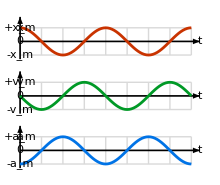

```mathematica
Block[{plt,d=4},
plt[f_,col_,var_]:={{AbsoluteThickness[1],LightGray,Translate[Line[{#,0}&/@{0,4π}],{0,#}]&/@{-1,1},Translate[Line[{0,#}&/@{-1,1}],{# π,0}]&/@Range[0,4,1/2]},{AbsoluteThickness[1.2],Arrow[{0,#}&/@{-1.3,1.8}],Arrow[{#,0}&/@{0,4.2π}]},{col,AbsoluteThickness[2],Line[Table[{t,f[t]},{t,0,4π,0.05π}]]},Text["\!\(t\)",{4.2π,0},{0,1}],Text[StringTemplate["\!\(+`1`\_m\)"][var],{0,1},{1.2,0}],Text[StringTemplate["\!\(-`1`\_m\)"][var],{0,-1},{1.2,0}],Text["\!\(0\)",{0,0},{1.5,0}],Text[StringTemplate["\!\(`1`\)"][var],{0,1},{-2,-1}]};
Graphics[{
Translate[plt[Cos[#]&,Red,"x"],{0,d}],
plt[-Sin[#]&,Green,"v"],
Translate[plt[-Cos[#]&,Blue,"a"],{0,-d}]},ImageSize->220]]
```

### 15-2

#### energy

```mathematica
Block[{plt,d=4},
plt[f_,col_,var_]:={{AbsoluteThickness[1],LightGray,Translate[Line[{#,0}&/@{0,4π}],{0,#}]&/@{-1,1},Translate[Line[{0,#}&/@{-1,1}],{# π,0}]&/@Range[0,4,1/2]},{AbsoluteThickness[1.2],Arrow[{0,#}&/@{-1.3,1.8}],Arrow[{#,0}&/@{0,4.2π}]},{col,AbsoluteThickness[2],Line[Table[{t,f[t]},{t,0,4π,0.05π}]]},Text["\!\(t\)",{4.2π,0},{0,1}],Text[StringTemplate["\!\(+`1`\_m\)"][var],{0,1},{1.2,0}],Text[StringTemplate["\!\(-`1`\_m\)"][var],{0,-1},{1.2,0}],Text["\!\(0\)",{0,0},{1.5,0}],Text[StringTemplate["\!\(`1`\)"][var],{0,1},{-2,-1}]};
Graphics[{
Translate[plt[Cos[#]&,Red,"x"],{0,d}],
plt[-Sin[#]&,Green,"v"],
Translate[{Block[{c},
c=Line[Table[{t,4Sin[t]^2},{t,0,4π,0.05π}]];
{{Lighter[Red,0.8],FilledCurve@{c,Line[{#,4}&/@{4π,0}]}},{Lighter[Green,0.8],FilledCurve@{c,Line[{#,0}&/@{4π,0}]}},{Gray,AbsoluteThickness[2],c}}],
{AbsoluteThickness[1],LightGray,Translate[Line[{#,0}&/@{0,4π}],{0,#}]&/@{0,4},Translate[Line[{0,#}&/@{0,4}],{# π,0}]&/@Range[0,4,1/2]},{AbsoluteThickness[1.2],Arrow[{0,#}&/@{0,4.8}],Arrow[{#,0}&/@{0,4.2π}]},
Text["\!\(E\)",{0,4.2},{2,0}],
Text["\!\(0\)",{0,0},{1.5,0}],
Text["\!\(t\)",{4.2π,0},{0,1}],{Red,Text["\!\(U\)",{π,2.5}]},{Green,Text["\!\(K\)",{π/2,1.5}]}},{0,-7}]},ImageSize->220]]
```

-Graphics-

### 15-3

#### objects

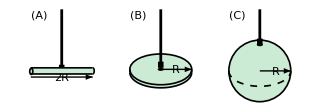

```mathematica
Block[{ah,holo,col,wire,rod,disk,ball},
ah[specs_]:=Arrowheads[{0.0001 #1,#2,Graphics[Line[Offset/@{{-5,-2},{0,0},{-5,2}}]]}&@@@specs];
wire[y_:0]:={AbsoluteThickness[2],Line[{0,#}&/@{y,2}],AbsoluteThickness[4],Line[{0,#}&/@{y,y+0.2}]};
col=Lighter[Green,0.8];
rod=Block[{a=0.1,b=0.05},{{col,Disk[{#,0},{b,a}]&/@{1,-1},Rectangle[{-1,-a},{1,a}]},{AbsoluteThickness[1.2],Circle[{-1,0},{b,a}],Circle[{1,0},{b,a},{-π/2,π/2}],Translate[Line[{#,0}&/@{-1,1}],{0,#}]&/@{-a,a}},Translate[{AbsoluteThickness[1],ah[{{-1,0},{1,1}}],Arrow[{#,0}&/@{-1,1}],Text["\!\(2R\)",{0,0},{0,1}]},{0,-a-0.1}]}];
disk=Block[{a=0.05,d=0.5},
{{col,Disk[{0,#},{1,d}]&/@{-a,a}},{AbsoluteThickness[1.2],Circle[{0,a},{1,d}],Circle[{0,-a},{1,d},{-π,0}],Translate[Line[{0,#}&/@{-a,a}],{#,0}]&/@{-1,1}},
{Black,Disk[{0,a},0.1{1,d}]},Translate[{AbsoluteThickness[1],ah[{{1,1}}],Arrow[{#,0}&/@{0,1}],Text["\!\(R\)",{0.5,0},{0,1}]},{0,a}]}];
ball=Block[{d=0.5},{{col,Disk[{0,0}]},{AbsoluteThickness[1.2],Circle[{0,0}],Dashed,Circle[{0,0},{1,d},{-π,0}]},{Black,Disk[{0,0.85},0.1{1,d}]},{AbsoluteThickness[1],ah[{{1,1}}],Arrow[{#,0}&/@{0,1}],Text["\!\(R\)",{0.5,0},{0,-0.8}]}}];
Graphics[{Translate[{wire[],rod,Text["(A)",{-1,2},{-1,1}]},{-3.2,0}],Translate[{disk,wire[0.1],Text["(B)",{-1,2},{-1,1}]},{0,0}],Translate[{ball,wire[0.85],Text["(C)",{-1,2},{-1,1}]},{3.2,0}]},ImageSize->320]]
```

### 15-5

#### damping

```mathematica
Block[{damp,h=3.8},
damp[τ_,col_,tlt_]:=Block[{ω=2π,γ,Ω,T=10,x},
γ=1/(2τ);Ω=Sqrt[ω^2-γ^2];
x[t_]:=Exp[-γ t](Cos[Ω t]+γ t Sinc[Ω t]);
{{AbsoluteThickness[1],Arrow[{#,0}&/@{0,T+0.5}],Arrow[{0,#}&/@{-1.2,1.7}],Text["\!\(t\)",{T,0},{-1,1}],Text["\!\(x\)",{0,1},{2,-1}],Text["0",{0,0},{1.2,0.2}]},
If[ω τ>1,{Lighter[col,0.8],Dashed,Scale[Line[Table[{t,Exp[-t/(2τ)]},{t,0,T,0.5}]],{1,#},{0,0}]&/@{1,-1}}],{col,Line[Table[{t,x[t]},{t,0,T,0.01}]]},{col,Text[tlt,{T/2,1},{0,-1}]}}];
Graphics[{Translate[damp[1000,Green,"Undamped"],{0,0}],Translate[damp[4/π,Orange,"Underdamped"],{0,-h}],Translate[damp[1/(4π),Red,"Critially damped"],{0,-2h}],Translate[damp[1/(32π),Blue,"Overdamped"],{0,-3h}]},ImageSize->220]]
```

-Graphics-

### 15-6

#### forced_oscillation

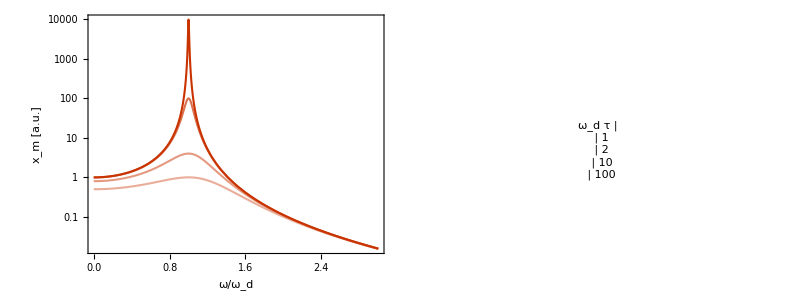

```mathematica
Block[{τs,cols},
τs={1,2,10,100};
cols=Lighter[Red,#]&/@{0.6,0.5,0.3,0};
Grid[{{LogPlot[Evaluate@Table[1/((x^2-1)^2+1/τ^2),{τ,τs}],{x,0,3},
BaselinePosition->Scaled[0.6],PlotStyle->cols,PlotRange->All,GridLines->{{1},Automatic},FrameLabel->{"\!\(ω/ω\_d\)","\!\(x\_m\) [a.u.]"},AspectRatio->0.5,ImageSize->280],
Graphics[Inset@Style[Grid@Prepend[{Graphics[{#1,Line[{#,0}&/@{0,1}]},AspectRatio->0.1,ImageSize->15],#2}&@@@Thread@{cols,τs},{Text[Style["\!\(ω\_d τ\)","InlineFormula"]],SpanFromLeft}],"InlineFormula"],
AspectRatio->1.5]}}]]
```

## Chap 32

### 32-1

#### manifolds

```mathematica
Block[{pts,bsf},
SeedRandom[6];
pts=Table[Block[{δr,δθ,δh},
{δr,δθ,δh}={0.2r^4,0.2π,0.2r^4}RandomReal[{-1,1},3];
{(r+δr) Cos[θ+δθ],(r+δr) Sin[θ+δθ],-0.5r^4Sin[θ]^2+δh }],{θ,0,3π/2,π/2},{r,{0,0.1,0.5,1}}];
bsf=BSplineFunction[pts,SplineClosed->{True,False}];
Graphics3D[{{Opacity[0.8],Lighter[Red,0.65],EdgeForm[Blue],BSplineSurface[pts,SplineClosed->{True,False}]},{Red,Text["\!\(Σ\)",{0.3,-0.4,-0.2}],Blue,Text["\!\(∂Σ\)",{0.25,-0.8,-0.55}]},
{Red,Arrowheads[0.05],Block[{n},n=Normalize[Cross[Derivative[0,1][bsf][##],Derivative[1,0][bsf][##]]];
Translate[Arrow[Tube[{{0,0,0},0.18n},0.01]],bsf[##]]]&@@@{{0,0.01},{0.8,0.7},{0.4,0.8}},Text["\!\(n\&^\)",bsf[0,0],{1.5,-0.8}]},{Blue,EdgeForm[None],Translate[Cone[{{0,0,0},0.12Normalize[bsf[#+0.001,1]-bsf[#,1]]},0.03],bsf[#-0.01,1]]&/@{0.4,0.7}}},Lighting->"Neutral",Boxed->False,ViewPoint->{1.6,-2,1.2},AspectRatio->1,ImageSize->100]]
```

-Graphics3D-

```mathematica
Block[{surf},
surf=Cases[ParametricPlot3D[(0.5+0.5Sin[θ]^4){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},Mesh->{5,Range[0,2π,π/4]+0.001}],
GraphicsComplex[pts_,p_,opts__]:>
{GraphicsComplex[pts,{{Opacity[0.8],Lighter[Red,0.7],EdgeForm[None],Cases[p,g_GraphicsGroup:>g,∞]},
{Red,Opacity[0.2],AbsoluteThickness[1],Dashed,Cases[p,_Line,∞]}},opts],
{Red,Arrowheads[0.04],Translate[Arrow[Tube[{{0,0,0},0.3#2},0.012]],#1]&@@@(Thread@{pts,OptionValue[opts,VertexNormals]})[[{1,6,11}]],
Text["\!\(n\&^\)",pts[[1]],{1.5,-1.5}]}},∞];
SeedRandom[0];
Graphics3D[{surf,{Red,Text["\!\(S\)",{1,0,0}]}},Lighting->{"Neutral",DirectionalLight[Gray,{2,-1,-2}]},Boxed->False,ViewPoint->{4,-2,2},PlotRange->All,AspectRatio->1,ImageSize->100]]
```

-Graphics3D-

```mathematica
Block[{pts},
SeedRandom[1];
pts=Table[{x,0,0}+0.2(x^2-1)RandomReal[{-1,1},3],{x,{-1,-0.5,0,0.5,1}}];
Graphics3D[{{Blue,Arrowheads[{0.06,#}&/@{0.3,0.8}],Arrow[Tube[BSplineCurve[pts],0.02]],Text["\!\(Γ\)",{0,0,0},{0,-1}],Text["\!\(ℓ\&^\)",{-0.6,0,0},{0,1}]},
{Purple,Point[{#,-0.1,0.1}]&/@{-1,1},Text["\!\(a\)",{-1,0,0},{0,-0.8}],Text["\!\(b\)",{1,0,0},{0,-0.8}]}},Lighting->"Neutral",Boxed->False,PlotRange->{{-1.1,1.1},{-1,1},{-1,1}},ViewPoint->{0,-4,4},AspectRatio->1,ImageSize->100]]
```

-Graphics3D-

```mathematica
Block[{pts},
SeedRandom[5];
pts=Table[{Cos[θ],Sin[θ],0}+0.2RandomReal[{-1,1},3],{θ,0,5π/6,π/6}];
Graphics3D[{{Blue,Arrowheads[{0.07,#}&/@{0,0.33,0.66}],Arrow[Tube[BSplineCurve[pts,SplineClosed->True],0.015]],Text["\!\(C\)",{0,0,0},{0,-0.8}],Text["\!\(ℓ\&^\)",{0,0,0},{-6,2.5}]}},Lighting->"Neutral",Boxed->False,ViewPoint->{1,2,4},AspectRatio->1,ImageSize->100]]
```

-Graphics3D-

##### Backup (with field lines)

```mathematica
Block[{pts},
SeedRandom[6];
pts=Table[Block[{δr,δθ,δh},
{δr,δθ,δh}={0.2r^4,0.2π,0.2r^4}RandomReal[{-1,1},3];
{(r+δr) Cos[θ+δθ],(r+δr) Sin[θ+δθ],-0.5r^4Sin[θ]^2+δh }],{θ,0,3π/2,π/2},{r,{0,0.1,0.5,1}}];
Graphics3D[{{Opacity[0.8],Lighter[Red,0.65],EdgeForm[Red],BSplineSurface[pts,SplineClosed->{True,False}]},{Red,Text["\!\(Σ\)",{0.3,-0.4,-0.2}],Text["\!\(∂Σ\)",{0.25,-0.8,-0.55}]},{Arrowheads[{{0.05}}],Black,Translate[Arrow[Tube[BSplineCurve[Table[{0,0,u}+0.1RandomReal[{-1,1},3],{u,{-1,-0.5,0.3}}]],0.01]],Append[#,0]]&/@RandomReal[{-0.7,0.3},{3,2}],
Text["\!\(F\&→\)",{-0.2,-0.3,0.1}]}},Lighting->"Neutral",Boxed->False,ViewPoint->{1.6,-2,1.2},ImageSize->100]]
```

-Graphics3D-

```mathematica
Block[{surf},
surf=Cases[ParametricPlot3D[(0.5+0.5Sin[θ]^4){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},Mesh->{5,Range[0,2π,π/4]+0.001}],
GraphicsComplex[pts_,p_,opts__]:>
GraphicsComplex[pts,{{Opacity[0.8],Lighter[Red,0.7],EdgeForm[None],Cases[p,g_GraphicsGroup:>g,∞]},
{Red,Opacity[0.2],AbsoluteThickness[1],Dashed,Cases[p,_Line,∞]}},opts],∞];
SeedRandom[1];
Graphics3D[{surf,{Red,Text["\!\(S\)",{1,0,0}]},{Arrowheads[{{0.05}}],Black,Translate[Arrow[Tube[BSplineCurve@Table[{0,0,z}+0.2(z^2-1)RandomReal[{-1,1}],{z,{-1,0,1}}],0.014]],Append[0.5#,0]]&/@CirclePoints[3],Text["\!\(F\&→\)",{0,0,1}]}},Lighting->{"Neutral",DirectionalLight[Gray,{2,-1,-2}]},Boxed->False,ViewPoint->{4,-2,2},PlotRange->All,ImageSize->100]]
```

-Graphics3D-

### 32-2

#### surface_loop

```mathematica
Block[{f,p,S,a=0.006},
f=BSplineFunction[{{1,-0.2},{0,0.8},{-1,0},{-0.5,-0.8}},SplineClosed->True];
p[u_,v_]:=Append[v f[u],0.5(1-v^2)];
S=Cases[ParametricPlot3D[p[u,v],{u,0,1},{v,0,1},PlotStyle->Directive[Lighter[Red,0.65],Opacity[0.8]],Mesh->None,PlotPoints->{64,5}],_GraphicsComplex,∞];
Graphics3D[{{S,{Red,Text["\!\(Σ\)",{0,0,0.5},{0,1}]}},{Blue,Arrowheads[{{0.05,0.5}}],Arrow[Tube[Table[p[u,1],{u,0,1,0.01}],a]],Text["\!\(C=∂Σ\)",p[0.55,1],{-1,1}],Text["\!\(d s\&→\)",p[0.5,1],{0,-1}]},
Block[{u0,v0,n},{u0,v0}={0.6,0.6};n=-0.2Normalize@Cross[p[u0+0.01,v0]-p[u0,v0],p[u0,v0+0.01]-p[u0,v0]];
{Translate[{Red,Arrow[Tube[{{0,0,0},n},a]],Text["\!\(d A\&→\)",n,{-0.8,-0.8}]},p[u0,v0]],{Red,AbsoluteThickness[1.2],Line[p@@@Table[{u0,v0}+0.05{0.4,1}(Sign[#]Abs[#]^0.1&/@{Cos[θ],Sin[θ]}),{θ,0,2π,0.01π}]]}}]},Lighting->"Neutral",Boxed->False,Axes->False,ViewPoint->{-1., -2.5, 0.8},ImageSize->180]]
```

-Graphics3D-

#### capacitor

```mathematica
Table[Block[{a=0.1,b=0.3,c=-0.3,d=0.5,e=-0.3},
Graphics[{{Red,Dashed,BSplineCurve[If[t==1,{{c,d},{0,0.9d},{0,0.6d},{0,-0.6d},{0,-0.9d},{c,-d}},{{c,d},{e,0.9d},{e,0.6d},{e,-0.6d},{e,-0.9d},{c,-d}}]],
Text["\!\(Σ\)",If[t==1,{0,-0.9d},{e+0.05,-0.2d}]]},
{Blue,Text[Style[#1,Background->White],{c,#2 d}]&@@@{{"⊙",+1},{"⊗",-1}},Text["\!\(C\)",{c,# d},{2,0}]&/@{1,-1}},{Green,Arrowheads[{{0.01,0.75,Graphics[Line[Offset/@{{-2,2},{2,0},{-2,-2}}]]}}],AbsoluteThickness[1.2],Table[Translate[Arrow[Table[{x,0.04(y/b)^5Cos[π /2 (x/a)]},{x,a Range[-1,1,0.1]}]],{0,y}],{y,b Range[-1,1,0.4]}],
Text["\!\(E\&→\)",{0,b},{-1.5,-1.2}]},{Arrowheads[{{0.05,0.55}}],Arrow[{#,0}&/@{-1,-a}],Arrow[{#,0}&/@{a,0.5}],Text["\!\(i\)",{-0.55,0},{0,-1}]},{AbsoluteThickness[3],Translate[{Line[{0,#}&/@{-b,b}],{If[#<0,Red,Blue],Table[Text[Style[If[#<0,"+","-"],12],{0,y},{1.2Sign[#],0}],{y,b Range[-0.8,0.8,0.4]}]}},{#,0}]&/@{-a,a}}},ImageSize->180]],{t,0,1}]
```

{-Graphics-,-Graphics-}

### 32-6

#### loop_model

```mathematica
Block[{holo,t=0.2},
holo[txt_]:={{White,Translate[txt,0.04#]&/@CirclePoints[32]},txt};
Graphics[{{AbsoluteThickness[1],Scale[Translate[Rotate[Line[Offset/@(8{{1,0},{1,-1},{0,-1}})],{{1,0},{-1,t}}],{1,0}],{#,1},{0,0}]&/@{1,-1}},{Green,Table[Arrow[{{(1-t)x,-1},{(1+t)x,1}}],{x,-1.8,1.8,0.4}],Text["\!\(B\&→\)",{-0.33,-1},{0,-0.8}]},{Red,Translate[{Arrow[{{0,0},0.7{#,t}}],holo@Text["\!\(F\&→\)",0.7{#,t},{# 1.4,-0.8}]},{-#,0}]&/@{1,-1},Arrow[{{0,0},{0,0.3}}],holo@Text["\!\(F\&→\_tot\)",{0,0.3},{0,-1}]},{Blue,holo@Text["\!\(i L\&→\)",{#-0.1,0},{-1.5#,1}]&/@{1,-1},Line[{#,0}&/@{-1,1}],holo@Text["⊗",{-1,0}],holo@Text["⊙",{1,0}],Arrow[{{0,0},{0,-0.4}}],holo@Text["\!\(μ\&→\)",{0,-0.4},{-2,0.2}]}},ImageSize->180]]
```

-Graphics-

```mathematica
Block[{holo,t=0.2},
holo[txt_]:={{White,Translate[txt,0.04#]&/@CirclePoints[32]},txt};
Graphics[{{AbsoluteThickness[1],Scale[Translate[Rotate[Line[Offset/@(8{{1,0},{1,1},{0,1}})],{{1,0},{1,-t}}],{1,0}],{#,1},{0,0}]&/@{1,-1}},{Green,Table[Arrow[{{(1-t)x,-1},{(1+t)x,1}}],{x,-1.8,1.8,0.4}],Text["\!\(B\&→\)",{0,1},{0,0.8}]},{Red,Translate[{Arrow[{{0,0},0.7{#,-t}}],holo@Text["\!\(F\&→\)",0.7{#,-t},{0,1}]},{#,0}]&/@{1,-1},Arrow[{{0,0},{0,-0.3}}],holo@Text["\!\(F\&→\_tot\)",{0,-0.3},{0,1}]},{Blue,holo@Text["\!\(i L\&→\)",{#,0},{1.5#,-1}]&/@{1,-1},Line[{#,0}&/@{-1,1}],holo@Text["⊗",{1,0}],holo@Text["⊙",{-1,0}],Arrow[{{0,0},{0,0.4}}],holo@Text["\!\(μ\&→\)",{0,0.4},{-2,0.2}]}},ImageSize->180]]
```

-Graphics-

### 32-8

#### hysteresis

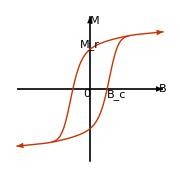

```mathematica
Block[{R=1.3,branch},
branch={Red,Arrowheads[{{0.001,0.6,Graphics[Line[Offset/@{{-2,-3},{2,0},{-2,3}}]]}}],Arrow[Table[{b,0.9Tanh[(5+3Tanh[2b])b]+0.1b},{b,-1,1,0.02}]]};
Graphics[{{Arrowheads[{{0.05,1}}],AbsoluteThickness[1.2],Arrow[ReIm@{-R,R}],Arrow[ReIm@{-ⅈ R,ⅈ R}],Text["0",{0,0},{1.5,1}],Text["\!\(B\)",{R,0},{0,1}],Text["\!\(M\)",{0,R},{-1.5,1}]},
Rotate[Translate[branch,{0.31,0.022}],#,{0,0}]&/@{0,π},
{Text["\!\(B\_c\)",{0.3,0},{-1,1}],Text["\!\(M\_r\)",{0,0.8},{1,0}]}},
ImageSize->180]]
```

## Chap 33

### 33-1

#### dipole_radiation

```mathematica
frames=Table[DipoleRadiationPlot[t],{t,0,47/48,1/48}];
ListAnimate[frames]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"32-3_dipole_radiation.mp4"}],frames,"FrameRate"->24,"VideoEncoding"->"H264"]
```

/Users/home/Documents/GitHub/everettyou.github.io/teaching/PHYS2C/notes_src/assets/figs/32-3_dipole_radiation.mp4

##### Definition

```mathematica
DipoleRadiationPlot[t_]:=Block[{ω=2π,L=1.5,Ψ,ag,Efield,Bfield,dipole},
Ψ[x_,y_]:=Block[{r,τ},
r=Sqrt[x^2+y^2+0.00001];τ=t-r;
(x/r)^2(Sin[ω τ]/r-ω Cos[ω τ])];
ag:=Line[Offset/@{{-2,-2},{2,0},{-2,2}}];
Efield=Cases[ContourPlot[Ψ[x,y],{x,0,L},{y,-L,L},Contours->{-3,3},ContourShading->None,ContourLabels->None,PlotPoints->15,PlotRange->{-5,5}],GraphicsComplex[pts_,p_]:>GraphicsComplex[pts,
Cases[p,Line[ids_]:>Block[{δ=0.01,level,norm,tang,sign,jds},
norm=({Ψ[#1+δ,#2],Ψ[#1,#2+δ]}-(level=Ψ[#1,#2]))&@@pts[[ids⟦1⟧]];
tang=#2-#1&@@pts[[ids[[{1,2}]]]];
sign=Sign@Det[{norm,tang}];
jds=If[sign>0,ids,Reverse[ids]];
Block[{f,fy,max,min,us,ah},
f=BSplineFunction[pts[[jds]]];
fy=BSplineFunction[pts[[jds,2]]];
{max,min}=Quiet@#[fy[Clip[u,{0,1}]],{u,0.5,0,1}]&/@{FindMaximum,FindMinimum};
us=DeleteDuplicates[Sort[Chop@{0.,u/.Last@max,
u/.Last@min,1.}],Abs[#1-#2]<0.0001&];
ah[u_]:=Block[{v},v=Normalize[f[Mod[u+δ,1]]-f[Mod[u,1]]];
Translate[Rotate[ag,{{1,0},v}],f[u]]];
{Purple,
Switch[Length[us],
2,ah[0.5],
_,If[Times@@(First/@{max,min})<0,
us=u/.(Quiet@FindRoot[fy[u],{u,(#1+#2)/2,#1,#2}]&@@@Thread@Through@{Most,Rest}@us);
ah/@Pick[us,#<1.&&Abs[fy[#]]<0.0001&/@us],
ah[If[level(#1-#2)>0,Min[#2/#1,0.1],Max[1-#1/#2,0.9]]&@@Abs[First/@{max,min}]]]],
Line[jds]}
]],∞]],∞];
Bfield[s_]:=Block[{δ=0.001,xs,pts,Bs},
xs=DeleteCases[DeleteDuplicates[x/.FindRoot[PowerExpand[Ψ[x,0]==0],{x,#}]&/@Prepend[(t-1/4+Range[Ceiling[0.5-2t],Floor[2L-2t+1.5]]/2),0.01],Abs[#1-#2]<δ&],x_/;x<0.1];
pts=Join[Table[ReIm[First@xs Exp[ⅈ θ]],{θ,-π/4,π/4,π/4}],Flatten[Table[ReIm[x Exp[ⅈ θ]],{θ,-3π/8,3π/8,π/8},{x,Rest@xs}],1]];
pts=DeleteCases[pts,{x_,y_}/;x<=0||x>=L];
Bs=Clip[Block[{n},
n={Ψ[#1+δ,#2],Ψ[#1,#2+δ]}/δ;
n.Normalize[{#1,#2}]/50]&@@@pts,{-1,1}];
Translate[
{Lighter[Green,1-Abs[#1]],Text[If[#1s>0,"⊙","⊗"]]},#2]&@@@Thread@{Bs,pts}];
dipole=Block[{d=0.05,p=Sin[ω t]},
{Opacity[Abs[p]],Translate[{Red,Disk[{0,0},d],{White,Text[Style["+",Bold],{0,0},{-0.1,0.05}]}},{0,d p}],Translate[{Blue,Disk[{0,0},d],{White,Text[Style["-",Bold],{0,0},{-0.1,0.05}]}},{0,-d p}]}];
Graphics[{Scale[{Bfield[#],Efield},{#,1},{0,0}]&/@{1,-1},dipole},PlotRange->{{-L,L},{-L,L}},ImageSize->300]];
```

```mathematica
DipoleRadiationPlot[0.34]
```

-Graphics-

#### LC_antenna

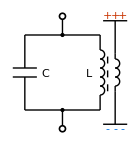

```mathematica
Block[{ZCh,ZC,ZL,SD},
ZCh=Block[{d=0.12,w=0.32},{Line[{0,#}&/@{d,1}],Line[{#,d}&/@{-w,w}]}];
ZC=Scale[ZCh,{1,#},{0,0}]&/@{1,-1};
ZL[l_,h_:1]:=Block[{r=0.12},{Table[Circle[{0,2r j},r,{-π/2,π/2}],{j,-l,l}],Line[{0,#}&/@{(2l+1)r,h}],Line[{0,#}&/@{-(2l+1)r,-h}]}];
SD=Block[{h=0.5,r=0.08}, {Line[{0,#}&/@{0,h}],{EdgeForm[Directive[AbsoluteThickness[1.2],Black]],White,Disk[{0,h},r]}}];
Graphics[{Translate[{Translate[ZC,{-1,0}],Translate[ZL[2],{1,0}],Translate[Line[{#,0}&/@{-1,1}],{0,#}]&/@{-1,1},
Scale[Translate[{SD,Point[{0,0}]},{0,1}],{1,#},{0,0}]&/@{1,-1}},{-1.2,0}],
{AbsoluteThickness[1],Dashed,Line[{0,#}&/@{-0.5,0.5}]},
Translate[{Scale[ZL[1,0.5],{-1,1},{0,0}],Scale[Translate[ZCh,{0,-1.5}],{1,#},{0,0}]&/@{1,-1},
Translate[{#1,Table[Text[#2,{0.2i,0}],{i,Range[-1,1]}]},{0,1.5 #3}]&@@@{{Red,"+",1},{Blue,"-",-1}}},{0.2,0}],
Text["\!\(C\)",{-1.65,-0.05}],Text["\!\(L\)",{-0.5,-0.05}]},ImageSize->140]
]
```